# Negative Curvature Directions

A negative curvature direction for 
	f(x)=0.5x.A.x+g.x
is any direction satisfying v.A.v<0.  We have found lots of Hessians at saddle points.  An optimization algorithm that uses negative curvature directions (i.e. not one that ignores negative curvature like BFGS, DFP, or the Cholesky Modified Newton algorithms) will escape from such a saddle if it picks up a negative curvature direction.

We can estimate the probability of finding a negative curvature direction by simply sampling from uniformly distributed vectors on the surface of a sphere.  The easiest way to do this is to simply normalize a vector drawn from a standard normal distribution.  This distribution is called a Haar distribution.

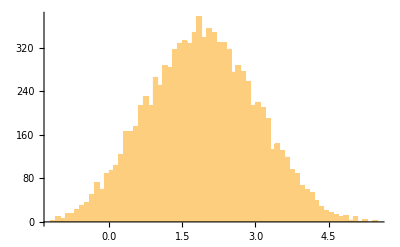

```mathematica
n=9; SampleSize=10^4;
A=RandomReal[{-1,1},{n,n}];A=A+Aᵀ+2IdentityMatrix[n];
Data1=Table[
v=Normalize[RandomVariate[NormalDistribution[0,1],n]];
v.A.v,{SampleSize}];
Histogram[Data1,60]
```

If we are careful to use a rotationally invariant distribution then since 
	A=Q.Λ.Qᵀ
where Q is the orthogonal matrix of eigenvectors and Λ is the diagonal matrix of eigenvalues we will get the same distribution by sampling from the diagonal matrix.

```mathematica
λs=Eigenvalues[A];
Λ=DiagonalMatrix[λs];
Data2=Table[
v=Normalize[RandomVariate[NormalDistribution[0,1],n]];
v.Λ.v,{SampleSize}];
PairedHistogram[Data1,Data2]
```

-Graphics-

The diagonal matrix is much simpler to understand. In particular, we can normalize after the matrix vector product and apply standard statistical tools to 
	v.Λ.v=(∑_(i=1)^n λ_i v_i^2)/(∑_(i=1)^n v_i^2)
We are interested in seeing the probability that v.A.v<0  which is identical to the probability that v.Λ.v<0 which is identical to the probability that 
	∑_(i=1)^n λ_i v_i^2<0.
This is simply a weighted sum of the squares of a set of n independent standard normally distributed random variables.  Fairly standard statistical techniques can be applied to this question.    With Ray Molzon’s help it should be able to translate the “Welch-Satherwaite” approximation to estimate this probability.  https://en.wikipedia.org/wiki/Welch%E2%80%93Satterthwaite_equation